```mathematica
Quit[];
```

```mathematica
<<Matchete`
```

v0.1.5

by Javier Fuentes-Martín, Matthias König, Julie Pagès, Anders Eller Thomsen, and Felix Wilsch 
Reference: [arXiv:2212.04510](https://arxiv.org/abs/2212.04510)
Website: https://gitlab.com/matchete/matchete

## Definition of the model

### Gauge group, fields and coupling

Define gauge group

```mathematica
DefineGaugeGroup[SU3c,SU[3],gs,G,FundAlphabet->{"a","b","c","d","e","f"},AdjAlphabet->{"A","B","C","D","E","F"}]
```

Define fields

```mathematica
DefineField[t,Fermion,Indices->{SU3c[fund]},Mass->{Light,MT}]
DefineField[u,Fermion,Indices->{SU3c[fund]},Mass->{Light,0}]
DefineField[sT,Scalar, Indices->{SU3c[fund]},Mass->{Heavy,mST}]
DefineField[chi, Fermion, Mass->{Heavy,mChi}]
```

Define coupling

```mathematica
DefineCoupling[yDM,SelfConjugate->True]
```

### Lagrangian

Write interactions

```mathematica
Lint=-yDM[] Bar@t[a]**PL**chi[] sT[a]//PlusHc;
```

Define Lagrangian

```mathematica
LUV=FreeLag[]+Lint;
LUV//NiceForm
CheckLagrangian[LUV]
```

-1/4(G^μνA)^2+D_μOverBar[sT]_aD_μsT^a-mST^2 OverBar[sT]_a sT^a+ⅈ(OverBar[chi]·γ_μ·D_μchi)-mChi(OverBar[chi]·chi)+ⅈ((t̄)_a·γ_μ·D_μt^a)-MT((t̄)_a·t^a)+ⅈ((ū)_a·γ_μ·D_μu^a)-yDM OverBar[sT]_a(OverBar[chi]·P_R·t^a)-yDM sT^a((t̄)_a·P_L·chi)

True

Lagrangian of only light degrees of freedom

```mathematica
Llight= FreeLag[t,u,G];
%//NiceForm
```

-1/4(G^μνA)^2+ⅈ((t̄)_a·γ_μ·D_μt^a)-MT((t̄)_a·t^a)+ⅈ((ū)_a·γ_μ·D_μu^a)

## Matching to the effective Lagrangian

### One-loop

#### Matching

```mathematica
LEFTall=Match[LUV,LoopOrder->1,EFTOrder->6];
LEFT =( LEFTall-(LEFTall/.{yDM->0}))//CollectOperators; (* Just keep contributions from the BSM coupling *)
LEFT//NiceForm
```

ℏ (ⅈ/4 1/ϵ yDM^2+ⅈ/8 yDM^2 (1+2LF_(2,1,-1)[mST,mChi]))((t̄)_a·γ_μ P_R·D_μt^a)+ℏ (-ⅈ/4 1/ϵ yDM^2-ⅈ/8 yDM^2 (1+2LF_(2,1,-1)[mST,mChi]))(D_μ(t̄)_a·γ_μ P_R·t^a)+ⅈ/6 ℏ yDM^2 (LF_(3,1,-1)[mST,mChi]-LF_(4,1,-2)[mST,mChi])((t̄)_a·γ_μ P_R·D_μD^2t^a)+ⅈ/6 ℏ yDM^2 (LF_(3,1,-1)[mST,mChi]-LF_(4,1,-2)[mST,mChi])((t̄)_a·γ_μ P_R·D_νD_μD_νt^a)+ⅈ/6 ℏ yDM^2 (LF_(3,1,-1)[mST,mChi]-LF_(4,1,-2)[mST,mChi])((t̄)_a·γ_μ P_R·D^2D_μt^a)-ⅈ/6 ℏ yDM^2 (LF_(3,1,-1)[mST,mChi]-LF_(4,1,-2)[mST,mChi])(D^2D_ν(t̄)_a·γ_ν P_R·t^a)-ⅈ/6 ℏ yDM^2 (LF_(3,1,-1)[mST,mChi]-LF_(4,1,-2)[mST,mChi])(D_μD_νD_μ(t̄)_a·γ_ν P_R·t^a)-ⅈ/6 ℏ yDM^2 (LF_(3,1,-1)[mST,mChi]-LF_(4,1,-2)[mST,mChi])(D_μD^2(t̄)_a·γ_μ P_R·t^a)-1/6 ℏgs yDM^2 D_νG^μνA((t̄)_a·γ_μ P_R·t^b)T_b^Aa LF_(3,1,-1)[mST,mChi]+1/8 ℏ yDM^4((t̄)_a·γ_μ P_R·t^b)((t̄)_b·γ_μ P_R·t^a)LF_(2,2,-1)[mChi,mST]

#### Removing redundant operators off-shell

Simplify to the Green basis using integration by parts and collect Hermitian conjugate terms in + H.c.

```mathematica
LEFTOffShell=LEFT //GreensSimplify;
LEFTOffShell//HcSimplify //NiceForm
```

ℏ (ⅈ/2 1/ϵ yDM^2+ⅈ/4 yDM^2 (1+2LF_(2,1,-1)[mST,mChi]))((t̄)_a·γ_μ P_R·D_μt^a)+(ⅈ/2 ℏ yDM^2 (LF_(3,1,-1)[mST,mChi]-LF_(4,1,-2)[mST,mChi])(D^2(t̄)_a·γ_ν P_R·D_νt^a)+H.c.)-1/6 ℏgs yDM^2 D_νG^μνA((t̄)_a·γ_μ P_R·t^b)T_b^Aa LF_(4,1,-2)[mST,mChi]+1/8 ℏ yDM^4((t̄)_a·γ_μ P_R·t^b)((t̄)_b·γ_μ P_R·t^a)LF_(2,2,-1)[mChi,mST]

```mathematica
Simplify[IBPIdentities[{Bar@t,t},3]]//NiceForm
```

{((t̄)_a·γ_μ γ_ν γ_ρ P_R·D_μD_νD_ρt^a)→1/4 (-2(D_μ(t̄)_a·γ_μ P_R·D^2t^a)+2(D^2(t̄)_a·γ_ν P_R·D_νt^a)+ⅈ (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)+(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA T_b^Aa),(D_μD_νD_ρ(t̄)_a·γ_ρ γ_ν γ_μ P_R·t^a)→-ⅈ/4 (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)+(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA T_b^Aa+1/2 ((D_μ(t̄)_a·γ_μ P_R·D^2t^a)-(D^2(t̄)_a·γ_ν P_R·D_νt^a)),((t̄)_a·γ_μ γ_ν γ_ρ P_R·D_νD_μD_ρt^a)→1/4 (-2(D_μ(t̄)_a·γ_μ P_R·D^2t^a)+2(D^2(t̄)_a·γ_ν P_R·D_νt^a)-ⅈ (3((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)-(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA T_b^Aa),((t̄)_a·γ_μ γ_ν γ_ρ P_R·D_μD_ρD_νt^a)→1/4 (-2(D_μ(t̄)_a·γ_μ P_R·D^2t^a)+2(D^2(t̄)_a·γ_ν P_R·D_νt^a)+ⅈ (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)-3(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA T_b^Aa),(D_μD_ν(t̄)_a·γ_ν γ_ρ γ_μ P_R·D_ρt^a)→1/4 (-2(D_μ(t̄)_a·γ_μ P_R·D^2t^a)+2(D^2(t̄)_a·γ_ν P_R·D_νt^a)+ⅈ (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)-3(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA T_b^Aa),(D_μD_νD_ρ(t̄)_a·γ_ρ γ_μ γ_ν P_R·t^a)→1/4 (-ⅈ (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)-3(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA T_b^Aa+2 ((D_μ(t̄)_a·γ_μ P_R·D^2t^a)-(D^2(t̄)_a·γ_ν P_R·D_νt^a))),(D_μD_νD_ρ(t̄)_a·γ_ν γ_ρ γ_μ P_R·t^a)→1/4 (ⅈ (3((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)-(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA T_b^Aa+2 ((D_μ(t̄)_a·γ_μ P_R·D^2t^a)-(D^2(t̄)_a·γ_ν P_R·D_νt^a))),(D_μ(t̄)_a·γ_ν γ_μ γ_ρ P_R·D_νD_ρt^a)→1/4 (ⅈ (3((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)-(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA T_b^Aa+2 ((D_μ(t̄)_a·γ_μ P_R·D^2t^a)-(D^2(t̄)_a·γ_ν P_R·D_νt^a))),((t̄)_a·γ_μ γ_ν γ_ρ P_R·D_νD_ρD_μt^a)→1/4 (-2(D_μ(t̄)_a·γ_μ P_R·D^2t^a)+2(D^2(t̄)_a·γ_ν P_R·D_νt^a)-ⅈ (4D_νG^μνA((t̄)_a·γ_μ P_R·t^b)+ (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)-3(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA)T_b^Aa),((t̄)_a·γ_μ γ_ν γ_ρ P_R·D_ρD_μD_νt^a)→1/4 (-2(D_μ(t̄)_a·γ_μ P_R·D^2t^a)+2(D^2(t̄)_a·γ_ν P_R·D_νt^a)-ⅈ (4D_νG^μνA((t̄)_a·γ_μ P_R·t^b)+ (-3((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)+(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA)T_b^Aa),(D_μD_ν(t̄)_a·γ_μ γ_ρ γ_ν P_R·D_ρt^a)→1/4 (-2(D_μ(t̄)_a·γ_μ P_R·D^2t^a)+2(D^2(t̄)_a·γ_ν P_R·D_νt^a)-ⅈ (4D_νG^μνA((t̄)_a·γ_μ P_R·t^b)+ (-3((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)+(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA)T_b^Aa),(D_μD_ν(t̄)_a·γ_ρ γ_ν γ_μ P_R·D_ρt^a)→1/4 (-2(D_μ(t̄)_a·γ_μ P_R·D^2t^a)+2(D^2(t̄)_a·γ_ν P_R·D_νt^a)-ⅈ (4D_νG^μνA((t̄)_a·γ_μ P_R·t^b)+ (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)-3(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA)T_b^Aa),(D_μD_νD_ρ(t̄)_a·γ_ν γ_μ γ_ρ P_R·t^a)→1/4 (ⅈ (4D_νG^μνA((t̄)_a·γ_μ P_R·t^b)+ (-3((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)+(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA)T_b^Aa+2 ((D_μ(t̄)_a·γ_μ P_R·D^2t^a)-(D^2(t̄)_a·γ_ν P_R·D_νt^a))),(D_μD_νD_ρ(t̄)_a·γ_μ γ_ρ γ_ν P_R·t^a)→1/4 (ⅈ (4D_νG^μνA((t̄)_a·γ_μ P_R·t^b)+ (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)-3(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA)T_b^Aa+2 ((D_μ(t̄)_a·γ_μ P_R·D^2t^a)-(D^2(t̄)_a·γ_ν P_R·D_νt^a))),(D_μ(t̄)_a·γ_ν γ_μ γ_ρ P_R·D_ρD_νt^a)→1/4 (ⅈ (4D_νG^μνA((t̄)_a·γ_μ P_R·t^b)+ (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)-3(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA)T_b^Aa+2 ((D_μ(t̄)_a·γ_μ P_R·D^2t^a)-(D^2(t̄)_a·γ_ν P_R·D_νt^a))),((t̄)_a·γ_μ γ_ν γ_ρ P_R·D_ρD_νD_μt^a)→ⅈ/4 (4D_νG^μνA((t̄)_a·γ_μ P_R·t^b)- (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)+(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA)T_b^Aa+1/2 (-(D_μ(t̄)_a·γ_μ P_R·D^2t^a)+(D^2(t̄)_a·γ_ν P_R·D_νt^a)),(D_μ(t̄)_a·γ_ν γ_ρ γ_μ P_R·D_νD_ρt^a)→1/4 (ⅈ (4D_νG^μνA((t̄)_a·γ_μ P_R·t^b)+ (-3((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)+(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA)T_b^Aa+2 ((D_μ(t̄)_a·γ_μ P_R·D^2t^a)-(D^2(t̄)_a·γ_ν P_R·D_νt^a))),(D_μD_ν(t̄)_a·γ_ρ γ_μ γ_ν P_R·D_ρt^a)→ⅈ/4 (4D_νG^μνA((t̄)_a·γ_μ P_R·t^b)- (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)+(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA)T_b^Aa+1/2 (-(D_μ(t̄)_a·γ_μ P_R·D^2t^a)+(D^2(t̄)_a·γ_ν P_R·D_νt^a)),(D_μD_νD_ρ(t̄)_a·γ_μ γ_ν γ_ρ P_R·t^a)→1/4 (-ⅈ (4D_νG^μνA((t̄)_a·γ_μ P_R·t^b)- (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)+(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA)T_b^Aa+2 ((D_μ(t̄)_a·γ_μ P_R·D^2t^a)-(D^2(t̄)_a·γ_ν P_R·D_νt^a))),(D_μ(t̄)_a·γ_ν γ_ρ γ_μ P_R·D_ρD_νt^a)→1/4 (-ⅈ (4D_νG^μνA((t̄)_a·γ_μ P_R·t^b)- (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)+(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA)T_b^Aa+2 ((D_μ(t̄)_a·γ_μ P_R·D^2t^a)-(D^2(t̄)_a·γ_ν P_R·D_νt^a))),((t̄)_a·γ_μ P_R·D_νD_μD_νt^a)→1/2 (-(D_μ(t̄)_a·γ_μ P_R·D^2t^a)+(D^2(t̄)_a·γ_ν P_R·D_νt^a)-ⅈD_νG^μνA((t̄)_a·γ_μ P_R·t^b)T_b^Aa),(D_μD_νD_μ(t̄)_a·γ_ν P_R·t^a)→1/2 ((D_μ(t̄)_a·γ_μ P_R·D^2t^a)-(D^2(t̄)_a·γ_ν P_R·D_νt^a)+ⅈD_νG^μνA((t̄)_a·γ_μ P_R·t^b)T_b^Aa),((t̄)_a·γ_μ P_R·D_μD^2t^a)→1/4 (-2(D_μ(t̄)_a·γ_μ P_R·D^2t^a)+2(D^2(t̄)_a·γ_ν P_R·D_νt^a)+ⅈ (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)-(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA T_b^Aa),((t̄)_a·γ_μ P_R·D^2D_μt^a)→1/4 (-2(D_μ(t̄)_a·γ_μ P_R·D^2t^a)+2(D^2(t̄)_a·γ_ν P_R·D_νt^a)-ⅈ (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)-(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA T_b^Aa),(D^2D_ν(t̄)_a·γ_ν P_R·t^a)→1/4 (-ⅈ (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)-(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA T_b^Aa+2 ((D_μ(t̄)_a·γ_μ P_R·D^2t^a)-(D^2(t̄)_a·γ_ν P_R·D_νt^a))),(D_μD^2(t̄)_a·γ_μ P_R·t^a)→1/4 (ⅈ (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)-(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA T_b^Aa+2 ((D_μ(t̄)_a·γ_μ P_R·D^2t^a)-(D^2(t̄)_a·γ_ν P_R·D_νt^a))),(D_μ(t̄)_a·γ_ν P_R·D_νD_μt^a)→1/2 ((D_μ(t̄)_a·γ_μ P_R·D^2t^a)-(D^2(t̄)_a·γ_ν P_R·D_νt^a)+ⅈD_νG^μνA((t̄)_a·γ_μ P_R·t^b)T_b^Aa),(D_μ(t̄)_a·γ_ν P_R·D_μD_νt^a)→1/4 (ⅈ (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)-(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA T_b^Aa+2 ((D_μ(t̄)_a·γ_μ P_R·D^2t^a)-(D^2(t̄)_a·γ_ν P_R·D_νt^a))),(D_μD_ν(t̄)_a·γ_ν P_R·D_μt^a)→1/4 (-2(D_μ(t̄)_a·γ_μ P_R·D^2t^a)+2(D^2(t̄)_a·γ_ν P_R·D_νt^a)+ⅈ (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)-(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA T_b^Aa),(D_μD_ν(t̄)_a·γ_μ P_R·D_νt^a)→1/2 (-(D_μ(t̄)_a·γ_μ P_R·D^2t^a)+(D^2(t̄)_a·γ_ν P_R·D_νt^a)-ⅈD_νG^μνA((t̄)_a·γ_μ P_R·t^b)T_b^Aa),G^μνA((t̄)_a·γ_ρ Γ_μν P_R·D_ρt^b)T_b^Aa→ (2D_νG^μνA((t̄)_a·γ_μ P_R·t^b)-G^μνA(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))T_b^Aa,D_ρG^μνA((t̄)_a·γ_ρ Γ_μν P_R·t^b)T_b^Aa→-2D_νG^μνA((t̄)_a·γ_μ P_R·t^b)T_b^Aa,G^μνA(D_ρ(t̄)_a·Γ_νμ γ_ρ P_R·t^b)T_b^Aa→ (2D_νG^μνA((t̄)_a·γ_μ P_R·t^b)-G^μνA((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b))T_b^Aa,D_ρG^μνA((t̄)_a·Γ_νμ γ_ρ P_R·t^b)T_b^Aa→-2D_νG^μνA((t̄)_a·γ_μ P_R·t^b)T_b^Aa,G^μνA((t̄)_a·γ_ρ γ_μ γ_ν P_R·D_ρt^b)T_b^Aa→ (2D_νG^μνA((t̄)_a·γ_μ P_R·t^b)-G^μνA(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))T_b^Aa,D_ρG^μνA((t̄)_a·γ_ρ γ_μ γ_ν P_R·t^b)T_b^Aa→-2D_νG^μνA((t̄)_a·γ_μ P_R·t^b)T_b^Aa,D_ρG^μνA((t̄)_a·γ_ν Γ_μρ P_R·t^b)T_b^Aa→-D_νG^μνA((t̄)_a·γ_μ P_R·t^b)T_b^Aa,G^μνA(D_ρ(t̄)_a·γ_ν γ_μ γ_ρ P_R·t^b)T_b^Aa→ (2D_νG^μνA((t̄)_a·γ_μ P_R·t^b)-G^μνA((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b))T_b^Aa,D_ρG^μνA((t̄)_a·γ_ν γ_μ γ_ρ P_R·t^b)T_b^Aa→-2D_νG^μνA((t̄)_a·γ_μ P_R·t^b)T_b^Aa,D_ρG^μνA((t̄)_a·Γ_μρ γ_ν P_R·t^b)T_b^Aa→D_νG^μνA((t̄)_a·γ_μ P_R·t^b)T_b^Aa,G^μνA((t̄)_a·γ_μ γ_ρ γ_ν P_R·D_ρt^b)T_b^Aa→1/2 (-2D_νG^μνA((t̄)_a·γ_μ P_R·t^b)+ (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)+(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA)T_b^Aa,G^μνA((t̄)_a·γ_ν Γ_μρ P_R·D_ρt^b)T_b^Aa→1/4 (-2D_νG^μνA((t̄)_a·γ_μ P_R·t^b)+ (3((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)+(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA)T_b^Aa,G^μνA(D_ρ(t̄)_a·γ_ν Γ_μρ P_R·t^b)T_b^Aa→1/4 (6D_νG^μνA((t̄)_a·γ_μ P_R·t^b)- (3((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)+(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA)T_b^Aa,G^μνA(D_ρ(t̄)_a·γ_ν γ_ρ γ_μ P_R·t^b)T_b^Aa→1/2 (-2D_νG^μνA((t̄)_a·γ_μ P_R·t^b)+ (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)+(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA)T_b^Aa,G^μνA((t̄)_a·Γ_μρ γ_ν P_R·D_ρt^b)T_b^Aa→1/4 (-6D_νG^μνA((t̄)_a·γ_μ P_R·t^b)+ (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)+3(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA)T_b^Aa,G^μνA(D_ρ(t̄)_a·Γ_μρ γ_ν P_R·t^b)T_b^Aa→1/4 (2D_νG^μνA((t̄)_a·γ_μ P_R·t^b)- (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)+3(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA)T_b^Aa,D_ρG^μνA((t̄)_a·γ_μ γ_ρ γ_ν P_R·t^b)T_b^Aa→0,G^μνA((t̄)_a·γ_μ P_R·D_νt^b)T_b^Aa→1/4 (-2D_νG^μνA((t̄)_a·γ_μ P_R·t^b)+ (-((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)+(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA)T_b^Aa,G^μνA(D_μ(t̄)_a·γ_ν P_R·t^b)T_b^Aa→1/4 (2D_νG^μνA((t̄)_a·γ_μ P_R·t^b)+ (-((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)+(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA)T_b^Aa,(D_μ(t̄)_a·γ_μ γ_ν γ_ρ P_R·D_νD_ρt^a)→-ⅈ/4 (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)+(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA T_b^Aa+1/2 ((D_μ(t̄)_a·γ_μ P_R·D^2t^a)-(D^2(t̄)_a·γ_ν P_R·D_νt^a)),(D_μD_ν(t̄)_a·γ_ν γ_μ γ_ρ P_R·D_ρt^a)→1/4 (-2(D_μ(t̄)_a·γ_μ P_R·D^2t^a)+2(D^2(t̄)_a·γ_ν P_R·D_νt^a)+ⅈ (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)+(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA T_b^Aa),(D_μ(t̄)_a·γ_μ γ_ν γ_ρ P_R·D_ρD_νt^a)→1/4 (-ⅈ (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)-3(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA T_b^Aa+2 ((D_μ(t̄)_a·γ_μ P_R·D^2t^a)-(D^2(t̄)_a·γ_ν P_R·D_νt^a))),(D_μD_ν(t̄)_a·γ_μ γ_ν γ_ρ P_R·D_ρt^a)→1/4 (-2(D_μ(t̄)_a·γ_μ P_R·D^2t^a)+2(D^2(t̄)_a·γ_ν P_R·D_νt^a)-ⅈ (3((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)-(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA T_b^Aa),(D_μ(t̄)_a·γ_μ P_R·D^2t^a)→1/4 (-ⅈ (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)-(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA T_b^Aa+2 ((D_μ(t̄)_a·γ_μ P_R·D^2t^a)-(D^2(t̄)_a·γ_ν P_R·D_νt^a))),(D^2(t̄)_a·γ_ν P_R·D_νt^a)→1/4 (-2(D_μ(t̄)_a·γ_μ P_R·D^2t^a)+2(D^2(t̄)_a·γ_ν P_R·D_νt^a)-ⅈ (((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)-(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b))G^μνA T_b^Aa),G^μνA(D_ρ(t̄)_a·γ_ρ γ_μ γ_ν P_R·t^b)T_b^Aa→G^μνA(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b)T_b^Aa,G^μνA((t̄)_a·γ_ν γ_μ γ_ρ P_R·D_ρt^b)T_b^Aa→G^μνA((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)T_b^Aa,G^μνA(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b)T_b^Aa→G^μνA(D_ρ(t̄)_a·γ_ρ Γ_μν P_R·t^b)T_b^Aa,G^μνA((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)T_b^Aa→G^μνA((t̄)_a·Γ_νμ γ_ρ P_R·D_ρt^b)T_b^Aa}

```mathematica
LEFTsimp=(LEFTOffShell)/.{hbar->1/(16 Pi^2)}//CollectOperators ;
%//NiceForm
```

(ⅈ/32 1/π^2 1/ϵ yDM^2+ⅈ/64 1/π^2 yDM^2 (1+2LF_(2,1,-1)[mST,mChi]))((t̄)_a·γ_μ P_R·D_μt^a)-ⅈ/32 1/π^2 yDM^2 (LF_(3,1,-1)[mST,mChi]-LF_(4,1,-2)[mST,mChi])(D_μ(t̄)_a·γ_μ P_R·D^2t^a)+ⅈ/32 1/π^2 yDM^2 (LF_(3,1,-1)[mST,mChi]-LF_(4,1,-2)[mST,mChi])(D^2(t̄)_a·γ_ν P_R·D_νt^a)-1/96 1/π^2 gs yDM^2 D_νG^μνA((t̄)_a·γ_μ P_R·t^b)T_b^Aa LF_(4,1,-2)[mST,mChi]+1/128 1/π^2 yDM^4((t̄)_a·γ_μ P_R·t^b)((t̄)_b·γ_μ P_R·t^a)LF_(2,2,-1)[mChi,mST]

```mathematica
A1 = SelectOperatorClass[LEFTsimp,{Bar@t,t},1];
A1//NiceForm
(* Pick up only one of the terms (the other one is the h.c.) *)A2= SelectOperatorClass[LEFTsimp,{Bar@t,t},3]/.{gs->0}/.{(Bar[Field[t,Fermion,{d_},{e_,f_}]]**DiracProduct[c_,Proj[1]]**Field[t, Fermion, {b_},{Index[a_,Lorentz]}])->0};
A2//NiceForm
(* Pick up only the term of the gauge tensor *)
A3= SelectOperatorClass[LEFTsimp,{Bar@t,t},3]-(SelectOperatorClass[LEFTsimp,{Bar@t,t},3]/.{gs->0});
A3//NiceForm
```

(ⅈ/32 1/π^2 1/ϵ yDM^2+ⅈ/64 1/π^2 yDM^2 (1+2LF_(2,1,-1)[mST,mChi]))((t̄)_a·γ_μ P_R·D_μt^a)

-ⅈ/32 1/π^2 yDM^2 (LF_(3,1,-1)[mST,mChi]-LF_(4,1,-2)[mST,mChi])(D_μ(t̄)_a·γ_μ P_R·D^2t^a)

-1/96 1/π^2 gs yDM^2 D_νG^μνA((t̄)_a·γ_μ P_R·t^b)T_b^Aa LF_(4,1,-2)[mST,mChi]

### Explicit Expressions

```mathematica
A1exp=Collect[FullSimplify[EvaluateLoopFunctions[A1]/.{Log[μbar2/Coupling[mChi,{},0]^2]->Log[μbar2/Coupling[mST,{},0]^2]+Log[Coupling[mST,{},0]^2/Coupling[mChi,{},0]^2]}] ,{ϵ,Log[a_]},Simplify];
A1exp//NiceForm
```

ⅈ/32 1/π^2 1/ϵ yDM^2((t̄)_a·γ_μ P_R·D_μt^a)+ⅈ/64 1/π^2 yDM^2 (3 mChi^2-mST^2)((t̄)_a·γ_μ P_R·D_μt^a)1/(mChi^2-mST^2)+ⅈ/32 1/π^2 yDM^2((t̄)_a·γ_μ P_R·D_μt^a)Log[(μ̄)^2/mST^2]+ⅈ/32 1/π^2 mChi^4 yDM^2((t̄)_a·γ_μ P_R·D_μt^a)1/((mChi^2-mST^2)^2)Log[1/mChi^2 mST^2]

```mathematica
A2exp=Collect[FullSimplify[EvaluateLoopFunctions[A2]/.{Log[μbar2/Coupling[mChi,{},0]^2]->Log[μbar2/Coupling[mST,{},0]^2]+Log[Coupling[mST,{},0]^2/Coupling[mChi,{},0]^2]}] ,{mChi,mST},Simplify];
A2exp//NiceForm
```

ⅈ/192 1/π^2 yDM^2 (2 mChi^6-6 mChi^2 mST^4+mST^6+3 mChi^4 mST^2 (1+2Log[1/mChi^2 mST^2]))(D_μ(t̄)_a·γ_μ P_R·D^2t^a)1/((mChi^2-mST^2)^4)

```mathematica
A3exp=Collect[FullSimplify[EvaluateLoopFunctions[A3]/.{Log[μbar2/Coupling[mChi,{},0]^2]->Log[μbar2/Coupling[mST,{},0]^2]+Log[Coupling[mST,{},0]^2/Coupling[mChi,{},0]^2]}] ,{mChi,mST},Simplify];
A3exp//NiceForm
```

-1/576 1/π^2 gs yDM^2 (-18 mChi^4 mST^2+9 mChi^2 mST^4-2 mST^6+mChi^6 (11+6Log[1/mChi^2 mST^2]))D_νG^μνA((t̄)_a·γ_μ P_R·t^b)T_b^Aa 1/((mChi^2-mST^2)^4)

#### Degenerate Mass Limit

```mathematica
Collect[Limit[A1exp/.{Coupling[a_,{},0]->a},mChi->mST],{ϵ},Simplify]//NiceForm
```

ⅈ/32 1/π^2 yDM^2 1/ϵ((t̄)_a·γ_μ P_R·D_μt^a)+ⅈ/32 1/π^2 yDM^2((t̄)_a·γ_μ P_R·D_μt^a)Log[(μ̄)^2/mST^2]

```mathematica
Collect[Limit[A2exp/.{Coupling[a_,{},0]->a},mChi->mST],{ϵ},Simplify]//NiceForm
```

ⅈ/384 1/mST^2 1/π^2 yDM^2(D_μ(t̄)_a·γ_μ P_R·D^2t^a)

```mathematica
Collect[Limit[A3exp/.{Coupling[a_,{},0]->a},mChi->mST],{ϵ},Simplify]//NiceForm
```

1/384 gs 1/mST^2 1/π^2 yDM^2 D_νG^μνA((t̄)_a·γ_μ P_R·t^b)T_b^Aa

## Removing redundant operators on-shell

Simplify to the physical basis using field redefinitions. Scalar and fermion kinetic terms are canonically normalized.

```mathematica
LEFTOnShell=LEFT //EOMSimplify;
LEFTOnShellSimp=(LEFTOnShell//Matchete`PackageScope`ProjExpand//CollectOperators);
%//NiceForm
```

(-1/4+ℏ (-1/24 1/ϵ gs^2-1/24 gs^2 Log[(μ̄)^2/mST^2]))(G^μνA)^2+ⅈ((t̄)_a·γ_μ·D_μt^a)+ (-MT+ℏ (1/4 1/ϵ MT yDM^2+1/8 MT yDM^2 (1+2LF_(2,1,-1)[mST,mChi]-4 MT^2 (LF_(3,1,-1)[mST,mChi]-LF_(4,1,-2)[mST,mChi]))))((t̄)_a·t^a)+ⅈ((ū)_a·γ_μ·D_μu^a)+1/360 ℏ gs^3 1/mST^2 G^μνB G^μρC G^νρA f^ABC+ⅈ/4 ℏgsMT yDM^2 (LF_(3,1,-1)[mST,mChi]-LF_(4,1,-2)[mST,mChi])G^μνA((t̄)_a·Γ_μν·t^b)T_b^Aa+1/480 ℏ (-2 gs^4 1/mST^2+15 yDM^4 LF_(2,2,-1)[mChi,mST]-20 gs^2 yDM^2 LF_(4,1,-2)[mST,mChi])((t̄)_a·γ_μ·t^b)((t̄)_b·γ_μ·t^a)+1/720 ℏ gs^2 (gs^2 1/mST^2+10 yDM^2 LF_(4,1,-2)[mST,mChi])((t̄)_a·γ_μ·t^a)((t̄)_b·γ_μ·t^b)+1/48 ℏ (3 yDM^4 LF_(2,2,-1)[mChi,mST]-2 gs^2 yDM^2 LF_(4,1,-2)[mST,mChi])((t̄)_a·γ_μ·t^b)((t̄)_b·γ_μ γ_5·t^a)+1/32 ℏ yDM^4((t̄)_a·γ_μ γ_5·t^b)((t̄)_b·γ_μ γ_5·t^a)LF_(2,2,-1)[mChi,mST]+1/72 ℏ gs^2 yDM^2((t̄)_a·γ_μ·t^a)((t̄)_b·γ_μ γ_5·t^b)LF_(4,1,-2)[mST,mChi]+1/120 ℏ gs^2 (-gs^2 1/mST^2-5 yDM^2 LF_(4,1,-2)[mST,mChi])((t̄)_a·γ_μ·t^b)((ū)_b·γ_μ·u^a)-1/24 ℏ gs^2 yDM^2((t̄)_a·γ_μ γ_5·t^b)((ū)_b·γ_μ·u^a)LF_(4,1,-2)[mST,mChi]-1/240 ℏ gs^4 1/mST^2((ū)_a·γ_μ·u^b)((ū)_b·γ_μ·u^a)+1/360 ℏ gs^2 (gs^2 1/mST^2+5 yDM^2 LF_(4,1,-2)[mST,mChi])((t̄)_a·γ_μ·t^a)((ū)_b·γ_μ·u^b)+1/72 ℏ gs^2 yDM^2((t̄)_a·γ_μ γ_5·t^a)((ū)_b·γ_μ·u^b)LF_(4,1,-2)[mST,mChi]+1/720 ℏ gs^4 1/mST^2((ū)_a·γ_μ·u^a)((ū)_b·γ_μ·u^b)

```mathematica
cGTT=SelectOperatorClass[LEFTOnShellSimp/.{hbar->1/(16 Pi^2)},{Bar@t,t},2]//Matchete`PackageScope`ProjExpand//CollectOperators;
%//NiceForm
```

ⅈ/64 1/π^2 gsMT yDM^2 (LF_(3,1,-1)[mST,mChi]-LF_(4,1,-2)[mST,mChi])G^μνA((t̄)_a·Γ_μν·t^b)T_b^Aa

```mathematica
cGTTexp=FullSimplify[cGTT//EvaluateLoopFunctions,Assumptions->{mST>0,mChi>0,μbar2>0}];
%//NiceForm
```

-ⅈ/384 1/π^2 gsMT yDM^2 (2 mChi^6-6 mChi^2 mST^4+mST^6+3 mChi^4 mST^2 (1+2Log[1/mChi^2]-2Log[1/mST^2]))G^μνA((t̄)_a·Γ_μν·t^b)T_b^Aa 1/((mChi^2-mST^2)^4)

```mathematica
uuTT = SelectOperatorClass[LEFTOnShellSimp/.{hbar->1/(16 Pi^2)},{Bar@t,t,Bar@u,u},0]//Matchete`PackageScope`ProjExpand//CollectOperators;
uuTT = FullSimplify[uuTT-(uuTT/.{yDM->0})];
%//NiceForm
```

1/1152 1/π^2 gs^2 yDM^2 (-3 (((t̄)_a·γ_μ·t^b)+((t̄)_a·γ_μ γ_5·t^b))((ū)_b·γ_μ·u^a)+ (((t̄)_a·γ_μ·t^a)+((t̄)_a·γ_μ γ_5·t^a))((ū)_b·γ_μ·u^b))LF_(4,1,-2)[mST,mChi]

```mathematica
uuTTexp=FullSimplify[uuTT//EvaluateLoopFunctions,Assumptions->{mST>0,mChi>0,μbar2>0}];
%//NiceForm
```

1/6912 1/π^2 gs^2 yDM^2 (-18 mChi^4 mST^2+9 mChi^2 mST^4-2 mST^6+mChi^6 (11+6Log[1/mChi^2]-6Log[1/mST^2])) (-3 (((t̄)_a·γ_μ·t^b)+((t̄)_a·γ_μ γ_5·t^b))((ū)_b·γ_μ·u^a)+ (((t̄)_a·γ_μ·t^a)+((t̄)_a·γ_μ γ_5·t^a))((ū)_b·γ_μ·u^b))1/((mChi^2-mST^2)^4)

```mathematica
A0 = Simplify[-I cGTTexp/.{FieldStrength[a_,b_,c_,d_]->1,Bar[a_]->1,Field[a_,b_,c_,d_]->1,DiracProduct[a_]->1,CG[a_,b_]->1,Coupling[a_,b_,c_]->a}]
```

-(gs MT yDM^2 (-6 mChi^2 mST^4+3 mChi^4 mST^2 (2 log(1/mChi^2)-2 log(1/mST^2)+1)+2 mChi^6+mST^6))/(384 π^2 (mChi^2-mST^2)^4)

```mathematica
ScientificForm[A0/.{mST->400.,mChi->300.,yDM->10.,gs->√1.6336281,MT->172.}]
```

-2.22341×10^-5

```mathematica
ScientificForm[A0/.{mST->5000.,mChi->4500.,yDM->10.,gs->√1.6336281,MT->172.}]
```

-1.2577×10^-7

```mathematica
ScientificForm[A0/.{mST->5000.,mChi->4999.9,yDM->10.,gs->√1.6336281,MT->172.}]
```

0.

```mathematica
A0limit=Normal[Series[A0,{mChi,mST,1}]]
```

(gs MT yDM^2 (mChi-mST))/(960 π^2 mST^3)-(gs MT yDM^2)/(768 π^2 mST^2)

```mathematica
A0limit0=Normal[Series[A0,{mChi,mST,0}]]
```

-(gs MT yDM^2)/(768 π^2 mST^2)

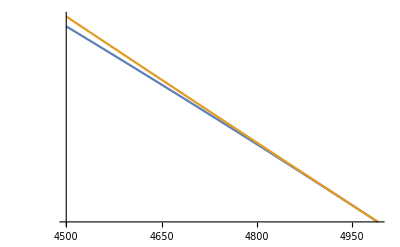

```mathematica
LogPlot[{A0limit/A0limit0/.{mST->5000.,yDM->10.,gs->√1.6336281,MT->172.},A0/A0limit0/.{mST->5000.,yDM->10.,gs->√1.6336281,MT->172.}},{mChi,4500,4990},PlotRange->All]
```

```mathematica
A0limit/.{mST->5000.,yDM->10.,gs->√1.6336281,MT->172.,mChi-> 4900.}
```

-1.17869×10^-7

```mathematica
A0limit/.{mST->5000.,yDM->10.,gs->√1.6336281,MT->172.,mChi-> 4900.}
```

-1.17869×10^-7